Your Title Here

```mathematica
w1=5;w2=7;h1=3;h2=5;L=2*(w1+w2);H=h1+h2;
```

```mathematica
truss=Graphics[{Thick,
{Thickness@#1,#2,Line[{{w2,0},{0.67*w2,h1}}],Line[{{w2,0},{w1+w2,H}}],Line[{{2*w1+w2,0},{L-0.67*w2,h1}}],Line[{{2*w1+w2,0},{w1+w2,H}}],Line[{{w1+w2,0},{w1+w2,H}}],
EdgeForm@{Thickness@#1,#2},FaceForm@None,Polygon[{{0,0},{L,0},{w1+w2,H}}]}&@@@{{0.015,Black},{0.01,GrayLevel@0.8}},

{GrayLevel@0.7,
Polygon[{{-0.7,-1},{0.7,-1},{0.5,0},{-0.5,0}}],Disk[{0,0},0.5],
Disk[{L,0},0.3],Disk[{L,-0.5},0.5],Polygon[{{L-0.275,0.12},{L+0.275,0.12},{L+0.47,-0.33},{L-0.47,-0.33}}]
},
{Thin,Line[{{-0.5,0},{-0.7,-1},{0.7,-1},{0.5,0}}],Line[{#,√(0.5^2-#^2)}&/@Range[-0.5,0.5,0.02]],
Line[{{L+#*0.275,0.12},{L+#*0.47,-0.33}}]&/@{-1,1},
Line[{#,√(0.3^2-(#-L)^2)}&/@Range[L-0.275,L+0.275,0.01]],Line[{#,-√(0.5^2-(#-L)^2)-0.5}&/@Range[L-0.5,L+0.5,0.01]],
Line[{#,√(0.5^2-(#-L)^2)-0.5}&/@Range[L-0.5,L-0.47,0.01]],Line[{#,√(0.5^2-(#-L)^2)-0.5}&/@Range[L+0.47,L+0.5,0.01]],
Line[{{#-1,-1},{#+1,-1}}]&/@{0,L}},

{PointSize@0.01,Point@{#,0}}&/@{0,L},

(*{Thin,
Line[{{0,0.25*h1},{0.67*w2,0.25*h1}}],Line[{{#,0.15*h1},{#,0.35*h1}}]&/@{0,0.67*w2},
Text[Style[Row@{"0.67",Subscript[Style[" w",Italic],2]},18,Background->White],{0.67*w2/2,0.25*h1}],

Line[{{0,-0.25*h1},{2*(w1+w2),-0.25*h1}}],Line[{{#,-0.15*h1},{#,-0.35*h1}}]&/@{0,w2,w1+w2,2*w1+w2,2*(w1+w2)},
Text[Style[Subscript[Style[" w",Italic],#1],18,Background->White],{#2,-0.25*h1}]&@@@{{2,w2/2},{1,w2+w1/2},{1,1.5*w1+w2},{2,2*w1+1.5*w2}},

Line[{{-0.25*h1,0},{-0.25*h1,h1+h2}}],Line[{{-0.15*h1,#},{-0.35*h1,#}}]&/@{0,h1,h1+h2},
Text[Style[Subscript[Style["h",Italic],#1],18,Background->White],{-0.25*h1,#2}]&@@@{{1,h1/2},{2,h1+h2/2}},

Line[{{-1.5,0},{0.66*w2-1.5,h1}}],Line[{{-1.3,0},{-1.7,0}}],Line[{{0.66*w2-1.3,h1},{0.66*w2-1.7,h1}}],
(*Text[Rotate[Style["√((SubscriptBox[h, 1])^2)",10,Background->White],ArcTan[h1/(0.6*w2)]],{0.6225,1.362}]*)
Text[Rotate[Style["z_1",18,Background->White],ArcTan[h1/(0.6*w2)]],{0.6225,1.362}]
}*)
},ImageSize->{600,400}];
```

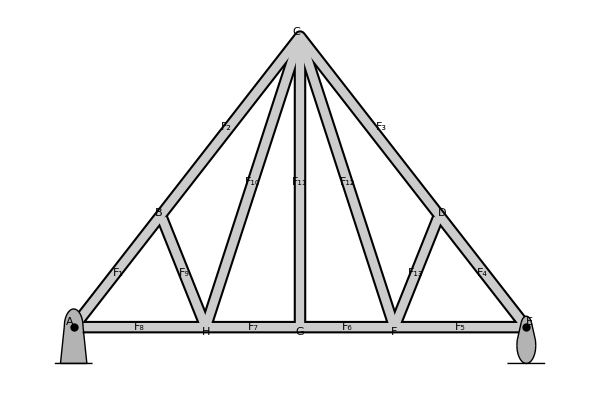

```mathematica
truss2=Graphics[{Thick,
{Thickness@#1,#2,Line[{{w2,0},{0.67*w2,h1}}],Line[{{w2,0},{w1+w2,H}}],Line[{{2*w1+w2,0},{L-0.67*w2,h1}}],Line[{{2*w1+w2,0},{w1+w2,H}}],Line[{{w1+w2,0},{w1+w2,H}}],
EdgeForm@{Thickness@#1,#2},FaceForm@None,Polygon[{{0,0},{L,0},{w1+w2,H}}]}&@@@{{0.015,Black},{0.01,GrayLevel@0.8}},

{GrayLevel@0.7,
Polygon[{{-0.7,-1},{0.7,-1},{0.5,0},{-0.5,0}}],Disk[{0,0},0.5],
Disk[{L,0},0.3],Disk[{L,-0.5},0.5],Polygon[{{L-0.275,0.12},{L+0.275,0.12},{L+0.47,-0.33},{L-0.47,-0.33}}]
},
{Thin,Line[{{-0.5,0},{-0.7,-1},{0.7,-1},{0.5,0}}],Line[{#,√(0.5^2-#^2)}&/@Range[-0.5,0.5,0.02]],
Line[{{L+#*0.275,0.12},{L+#*0.47,-0.33}}]&/@{-1,1},
Line[{#,√(0.3^2-(#-L)^2)}&/@Range[L-0.275,L+0.275,0.01]],Line[{#,-√(0.5^2-(#-L)^2)-0.5}&/@Range[L-0.5,L+0.5,0.01]],
Line[{#,√(0.5^2-(#-L)^2)-0.5}&/@Range[L-0.5,L-0.47,0.01]],Line[{#,√(0.5^2-(#-L)^2)-0.5}&/@Range[L+0.47,L+0.5,0.01]],
Line[{{#-1,-1},{#+1,-1}}]&/@{0,L}},

{PointSize@0.01,Point@{#,0}}&/@{0,L},

Text[Framed[Style[Row@{" ",#1," "},17],RoundingRadius->20],#2,1.5*#3]&@@@{{"A",{0,0},{1,-1}},{"B",{0.67*w2,h1},{2,-0.5}},{"C",{w1+w2,h1+h2},{1,-1}},{"D",{2*w1+1.33*w2,h1},{-1,-1}},{"E",{2*(w1+w2),0},{-1,-1}},{"F",{2*w1+w2,0},{0,1}},{"G",{w1+w2,0},{0,1}},{"H",{w2,0},{0,1}}},

(*Text[Framed[Style[Subscript[Style["F",Italic],#1],17],Background->White,FrameStyle->None,FrameMargins->Tiny],#2]&@@@{{"AB",{0.67*w2,h1}/2},{"AH",{w2/2,0}},{"BC",{0.8*w2+w1/2,h1+h2/2}},{"BH",{0.67*w2+0.33*w2/2,h1/2}},{"CH",{w2+w1/2,(h1+h2)/2}},{"CG",{w1+w2,(h1+h2)/2}},{"CF",{1.5*w1+w2,(h1+h2)/2}},{"CD",{2*w1+0.9*w2,h1+h2/2}},{"DE",{2*w1+1.67*w2,h1/2}},{"DF",{2*w1+w2+0.33*w2/2,h1/2}},{"EF",{2*w1+1.5*w2,0}},{"FG",{1.5*w1+w2,0}},{"GH",{w1/2+w2,0}}}*)

Text[Framed[Style[Subscript[Style["F",Italic],#1],17],Background->White,FrameStyle->None,FrameMargins->Tiny],#2]&@@@{{1,{0.67*w2,h1}/2},{8,{w2/2,0}},{2,{0.8*w2+w1/2,h1+h2/2}},{9,{0.67*w2+0.33*w2/2,h1/2}},{10,{w2+w1/2,(h1+h2)/2}},{11,{w1+w2,(h1+h2)/2}},{12,{1.5*w1+w2,(h1+h2)/2}},{3,{2*w1+0.9*w2,h1+h2/2}},{4,{2*w1+1.67*w2,h1/2}},{13,{2*w1+w2+0.33*w2/2,h1/2}},{5,{2*w1+1.5*w2,0}},{6,{1.5*w1+w2,0}},{7,{w1/2+w2,0}}}
},ImageSize->{600,400}]
```

```mathematica
{4.667,3}
```

```mathematica
4.667/w2
```

0.666714

```mathematica
3/h1
```

1

```mathematica
Manipulate[
Module[{θ1,z1,θ2,reactions,sol,RAx,RAy,RE,scale,forces,members},
θ1=ArcTan[h1/(0.33*w2)];z1=√(h1^2+(0.67*w2)^2);
θ2=ArcTan[h1/(0.67*w2)];

reactions=Quiet@Solve[{
rax+FA*Cos[θ1]==0,
z1*(-FA)+2*(w1+w2)*re+(w1+w2)*(-FB)==0,
ray-FA*Sin[θ1]+re-FB==0
},{rax,ray,re}][[1]];
RAx=rax/.reactions;RAy=ray/.reactions;RE=re/.reactions;

sol=Quiet@Solve[{
(*A*)
(*B*)
(*C*)
(*D*)
(*E*)
(*F*)
(*G*)
},{}][[1]];

scale[F_]:=1.5+5*Rescale[Abs@F,{0,10}];


forces={Blue,
If[FA≠0,Arrow[{{0.67*w2-scale[FA]*Cos[θ1],h1+scale[FA]*Sin[θ1]},{0.67*w2,h1}}]],
If[FB≠0,Arrow[{{w1+w2,h1+h2+scale[FB]},{w1+w2,h1+h2}}]],
If[#1≠0,Text[Style[Row@{NumberForm[#1,{3,1}]," kN"},18,Blue],#2,#3]]&@@@{{FA,{0.67*w2-scale[FA]*Cos[θ1],h1+scale[FA]*Sin[θ1]},{0.,-1}},{FB,{w1+w2,h1+h2+scale[FB]},{0,-1.5}}},
If[RAy≠0,Arrow[{{0,-scale[RAy]},{0,0}}]],If[RAx≠0,Arrow[{{-scale[RAx],0},{0,0}}]],
If[#1≠0,Text[Style[Row@{NumberForm[#1,{3,1}]," kN"},18],#2,#3]]&@@@{{RAx,{-scale[RAx],0},{1.1,0}},{RAy,{0,-scale[RAy]},{0,1.5}}},
If[RE≠0,Arrow[{{2*(w1+w2),-scale[RE]},{2*(w1+w2),0}}]],
If[RE≠0,Text[Style[Row@{NumberForm[RE,{3,1}]," kN"},18],{2*(w1+w2),-scale[RE]},{0,1.5}]]
};

members={
{Thickness@0.015,Red,CapForm@"Round",Switch[member,1,Line[{{0,0},{0.66*w2,h1}}],2,Line[{{0,0},{w2,0}}],3,Line[{{w2,0},{0.67*w2,h1}}],
4,Line[{{0.67*w2,h1},{w1+w2,H}}],5,Line[{{w2,0},{w1+w2,H}}],6,Line[{{w2,0},{w1+w2,0}}],7,Line[{{w1+w2,0},{w1+w2,H}}],
8,Line[{{w1+w2,H},{2*w1+w2+0.33*w2,h1}}],9,Line[{{w1+w2,H},{2*w1+w2,0}}],10,Line[{{w1+w2,0},{2*w1+w2,0}}],
11,Line[{{2*w1+w2,0},{2*w1+w2+0.33*w2,h1}}],12,Line[{{2*w1+w2+0.33*w2,h1},{L,0}}],13,Line[{{2*w1+w2,0},{L,0}}]]},

Text[Framed[Style[Row@{" ",#1," "},17],Background->White,RoundingRadius->15,FrameMargins->Tiny],#2]&@@@{{1,{0.66*w2/2,h1/2}},{2,{w2/2,0}},{3,{(0.67*w2+w2)/2,h1/2}},{4,{0.67*w2+(0.33*w2+w1)/2,h1+h2/2}},{5,{w2+w1/2,H/2}},{6,{w2+w1/2,0}},{7,{w1+w2,H/2}},{8,{w1+w2+(w1+0.33*w2)/2,h1+h2/2}},{9,{1.5*w1+w2,H/2}},{10,{1.5*w1+w2,0}},{11,{2*w1+w2+0.33*w2/2,h1/2}},{12,{2*w1+w2+(0.33*w2+w2)/2,h1/2}},{13,{2*w1+1.5*w2,0}}},
};

Show[truss,PlotRange->{{-7,25.7},{-6.8,15.8}}(*{{-11.5,27.5},{-7.4,15.8}}*),Epilog->{Thick,Arrowheads@0.045,forces,members}]
],
Grid[{
{Control[{{member,1,"member"},Range@13,PopupMenu}]},
{Style["point load forces (kN)",Bold],
Control[{{FA,2,"diagonal"},0,5,0.1,Appearance->"Labeled",ImageSize->Small}],
Control[{{FB,5,"vertical"},0,10,0.1,Appearance->"Labeled",ImageSize->Small}]}
},Alignment->Left],
SaveDefinitions->True]
```





```mathematica
Show[truss2,PlotRange->{{-7,26},{-6.8,15.8}},Epilog->{Thick,Blue,
Arrow[{{0.67*w2-scale[FA]*Cos[θ1],h1+scale[FA]*Sin[θ1]},{0.67*w2,h1}}],
Arrow[{{w1+w2,h1+h2+scale[FB]},{w1+w2,h1+h2}}],
Text[Style[Subscript[Style["F",Italic],#1],18,Blue],#2,#3]&@@@{{"A",{0.67*w2-scale[FA]*Cos[θ1],h1+scale[FA]*Sin[θ1]},{0.,-1}},{"B",{w1+w2,h1+h2+scale[FB]},{0,-1.5}}},
Arrow[{{0,-scale[RAy]},{0,0}}],Arrow[{{-scale[RAx],0},{0,0}}],
Text[Style[Subscript[Style["F",Italic],Row@{"A,",Style[#1,Italic]}],18],#2,#3]&@@@{{"x",{-scale[RAx],0},{1.1,0}},{"y",{0,-scale[RAy]},{0,1.5}}},
Arrow[{{2*(w1+w2),-scale[RE]},{2*(w1+w2),0}}],
Text[Style[Subscript[Style["F",Italic],"E"],18],{2*(w1+w2),-scale[RE]},{0,1.5}]
}]
```

Resize Images

Rotate and Zoom in 3D

Drag Locators

Create and Delete Locators

Slider Zoom

Gamepad Controls

Automatic Animation

Bookmark Animation

Contributed by: XXXX